# Li_2 Potentials

#### Constructing the X^1 Σ_g^+and a^3 Σ_u^+ potentials for Li_2 using the Morse/Long-Range Model [Le Roy et al. Chem. Phys. 131, 204309 (2009), Le Roy et al. Molecular Phys. 109, 3 (2011), and Le Roy and Dattani, Molecular Spectroscopy 268 (2011)]

The Morse/long-range (MLR) potential function is compact, requires relatively few parameters, allows for stable convergence in fits to experimental data, is well-behaved, and its parameters correspond to “key physically interesting properties” such as well depths, equilibrium distance, and long-range dispersion coefficients.

### The Morse/Long-Range Model for Potential Energy Functions

The basic MLR model for the radial potential energy function has the form,

V_MLR(r) = D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β(r) y_p(r))]^2

where D_e is the well depth, u_LR(r) is a function which describes the attractive long-range behavior V_LR(r) of the interaction to be,

V_LR(r) = D_e - u_LR(r)

and in general is given by a sum of inverse-power terms,

u_LR(r) = (∑^N)_(i =1)C_m_i/r^m_i= C_m_1/r^m_1+C_m_2/r^m_2+ ... + C_m_N/r^m_N.

The denominator factor in Eq. (1) u_LR(r_e) is the value of the function at the equilibrium length r_e. The radial behavior of u_LR(r) is expressed in terms of the dimensionless radial variable

y_p(r) = y_p^eq(r) =(r^p-r_e^p)/(r^p+r_e^p)

where the superscript "eq" denotes that we are using equilibrium bond length r_e and p is an integer greater than 1 whose value is partly defined (i.e., given a lower bound) by the choice of terms in u_LR(r). The exponent coefficient function β(r) is a slowly varying function of r and is expressed as a polynomial constrained to approach a specified value β_∞ as r →∞,

β(r) = y_p(r) β_∞ + [1 - y_p(r) ](∑^{N_s,N_L})_(i = 0) β_i(y_p(r))^i

where the to upper limits N_s and N_L specify the number of terms required for the sum in short- (r < r_e) and long-range (r > r_e) regions, respectively. By allowing the upper bounds of the summation in Eq.5 to be different in these two region, unphysical behavior, such as potential turnover, is prevent in the short-range region. However, it also means that there is a discontinuities in derivatives of the potential at r = r_e. 

The limiting behavior of Eq. (5) (i.e., β_∞) can be using Eq. (1) and Eq. (2),

V_MLR(r) = V(r), for r → ∞

D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β_∞)]^2 = D_e - u_LR(r)

D_e[1 -(2 e^(-β_∞))/(u_LR(r_e))u_LR(r) + e^(-2 β_∞)/(u_LR(r_e))^2(u_LR(r))^2] = D_e- u_LR(r)

D_e[1 -(2 e^(-β_∞))/(u_LR(r_e))u_LR(r)] ~ D_e- u_LR(r)

(2 D_e e^(-β_∞))/(u_LR(r_e))= 1

β_∞= ln((2 D_e)/(u_LR(r_e)))

Concerning the integer power “p” defining the radial variable of Eq. (4), it must be greater than the difference between the largest and smallest (inverse) powers of the terms included in the definition of u_LR(r) (i.e., p > m_N-m_i). In practice, it is often desirable to set p = m_(N+1)- m_i, where m_(N+1) is the next power predicted by theory that is not included in the chosen definition of u_LR(r), so that the leading contribution of the exponential term in Eq. (1) to the long-range potential u_LR(r) has the same radial behavior as the first missing term, 1/r^(m_(N+1)).

### Extensions of MLR model

##### 1. Addressing a problem associated with m_1= 3 long-range potentials

From Eq. (6), in the limit that r → ∞,  e^(-β_∞)= u_LR(r_e) / (2 D_e) and Eq. (1) thus becomes,

V_MLR(r) ~ D_e - u_LR(r) +(1/(4 D_e)[u_LR(r)])^2.

For a species, such as ground-state Li_2, which dissociates into two S-state atoms, theory tells us that the leading terms contributing to the long-range potential have powers m = 6, 8, 10. In this case, the leading contribution from the quadratic term in Eq. (7) would have an inverse power of 12 and thus, wouldn’t affect the limiting behavior defined by u_LR(r).

However, for a molecular state which dissociated to otherwise identical S- and P- state atoms, the long-range potential would also include a 1/r^3 term. In this case, substituting the two-term definition u_LR(r) = C_3/r^3+ C_6/r^6 into Eq. (7) will yield the long-range behavior,

V_MLR(r) ~ D_e-C_3/r^3-[C_6-(C_3)^2/(4 D_e)]/r^6+ (C_3 C_6/(2 D_e))/r^9+ ((C_6)^2/(4 D_e))/r^12.

The quadratic term introduces both a “fake” contribution to the overall 1/r^6 behavior and unphysical repulsive 1/r^9 and 1/r^12 terms. These problems can be fixed by defining u_LR(r) in a way that corrects for the modification of the effective C_6 value and addition of the 1/r^9 and 1/r^12 terms. If the C_6 coefficient is adjusted as (C^adj)_6= C_6 + (C_3)^2/(4 D_e), the coefficient of the 1/r^6 term in the long-range tail of the MLR potential given by Eq. (8) will be the desired C_6 value. The unphysical 1/r^9 term will disappear if a compensating adjusted 1/r^9 term is included in the definition of u_LR(r) with the coefficient (C^adj)_9= C_3(C^adj)_6/(2 D_e).

Problems due to the quadratic term in Eq. (7) arise when the leading term m_1 is such that second term is equal to m_1^2 or any subsequent terms are equal to sum of two proceeding terms. When these issues occur, the potential must be adjusted accordingly.

##### 2. Extending the definition of β(r) and y_p(r)

```mathematica
ypeq[p_,r_]:= (r^p - 1^p)/(r^p +1^p);
```

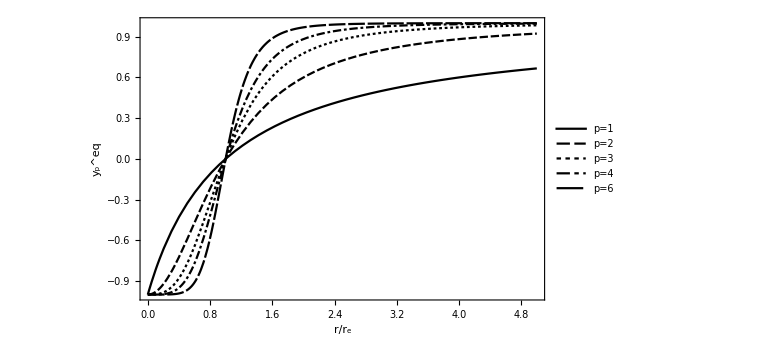

```mathematica
Plot[{ypeq[1,r],ypeq[2,r],ypeq[3,r],ypeq[4,r],ypeq[6,r]},{r,0,5},Frame->True, FrameLabel->{"r/r_e","y_p^eq"},LabelStyle->Large, ImageSize->Large, PlotLegends->{"p=1","p=2","p=3","p=4","p=6"}]
```

A problem associated with the use of y_p^eq(r) as the expansion variable in Eq. (5) is demonstrated by the graph above. With increasing values of p, the expansion variable y_p^eq(r) lies very close to the limiting value of +1 over an increasingly large fraction of the radial range. Over an interval within which y_p^eq(r) changes very little, a relatively high-order polynomial expansion in that variable would be required to provide an accurate description of any function which is not constant there. Mover, except in the highest values of p, y_p^eq(r) still differs significantly from the limiting value of -1 at the lower bound of the region, and thus a polynomial function of the variable could misbehave near this inner region.

One solution to this problem was introducing the use of different polynomial orders in Eq.(5) for the short- (r < r_e) and long-range (r > r_e) regions. However, this solution is not perfect, and introduces its own host of issues. For one as mentioned before there will be discontinuities in the potential at r_e. Moreover, the polynomial coefficients β_i for the smaller order sum usually have magnitudes of order ~ 1, while those of the other are often several orders of magnitude larger than that, and of oscillating sign.

All of these problems can be avoided if we express β(r) in terms of modified radial variable defined relative to a fixed reference distance r_ref>r_e,

y_p(r) = y_p^ref(r) =(r^p-r_ref^p)/(r^p+r_ref^p).

```mathematica
ypref[p_,r_]:= (r^p - 1.5^p)/(r^p +1.5^p);
```

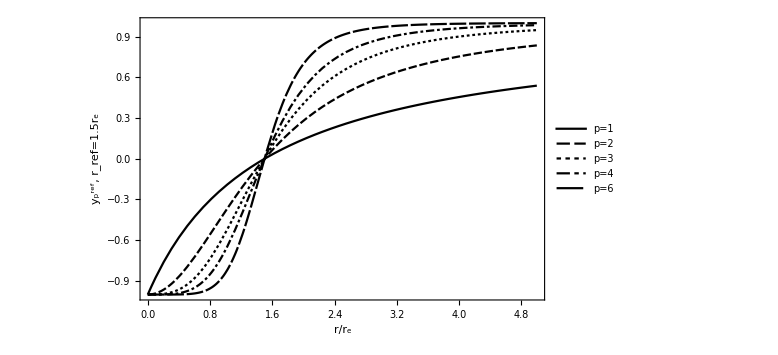

```mathematica
Plot[{ypref[1,r],ypref[2,r],ypref[3,r],ypref[4,r],ypref[6,r]},{r,0,5},Frame->True, FrameLabel->{"r/r_e","y_p^ref, r_ref=1.5r_e"},LabelStyle->Large, ImageSize->Large, PlotLegends->{"p=1","p=2","p=3","p=4","p=6"}]
```

For the case of r_ref=1.5 r_e as depicted in the figure above, the region over which y_p becomes flat and close to the +1 limit is pushed outward to substantially larger r. As a result, for appropriate choices of r_ref, the powers N_s and N_L in Eq. (5) may be set equal to one another (i.e., N_s=N_L), and lower-order polynomials can be used.

However y_p^eq(r) must still be used is the functional form of our MLR potential,

V_MLR(r) = D_e[1 - (u_LR(r))/(u_LR(r_e))e^(-β(r) y_p^eq(r))]^2

because the potential must take on the long-range form

V_MLR(r) ~ D_e - u_LR(r) +(1/(4 D_e)[u_LR(r)])^2

at the equilibrium distance r_e. This no precise method for choosing a value of r_ref but trial-and-error fits using r_ref/r_e~1.1-1.5 will guide one to an optimum choice for r_ref.

In cases in which multiple long-range terms are included in the definition of u_LR(r) (requiring p to be relatively large) and the turning points of the observed levels span a relatively large range of distances, quite high-order exponent polynomials are still required to yield a potential energy able to describe the system accurately. This due to the nature of the radial variable y_p^ref(r), which is still relatively flat at large r for relatively large p. A modification to our definition of the exponential coefficient β(r), given by Eq.(5), addresses this problem.

Examination of the asymptotic behavior of the exponential term in our MLR potential shows that if we introduce a second radial variable  y_q^ref(r) with q≠p, and rewrite β(r) as

β(r) =β_p^q(r) = y_p^ref(r) β_∞ + [1 - y_p^ref(r) ](∑^N)_(i = 0) β_i(y_q^ref(r))^i,

the leading correction to the limiting value (e^(-β_∞)) of the exponential involving the integer q has the form A_(p,q)/r^(p+q). This means that the value of the power q used to define the radial variable in the power series portion of  β_p^q(r)  does not affect the nature of the “leading deviation” from the limiting asymptotic value of the exponential term in Eq. (1) and q, therefore, can be given a relatively small value without causing any distortion of the long-range tail of the potential u_LR(r).

### Potential Energy Functions

For a molecule which dissociates into two S- state atoms, the leading terms in the long-range interaction potential have inverse powers m =6,8,10, and if they are ground-state atoms, the dispersion energy terms are all attractive. Thus, the long-range behavior of the X- state potential may be defined using a two- or three-term version of the function,

u_LR^X(r)  = C_6/r^6+ C_8/r^8+C_10/r^10.

### Born-Oppenheimer Breakdown Functions

It is necessary to take into account BOB effects that give rise to small differences between the rotationless potentials for different isotopologues, and to the small atomic-mass-dependent contributions to the rotational level energies. The vibration-rotation levels of isotopologue α of diatomic molecule A-B in a given electronic state are the eigenvalues of the radial Schrodinger equation

{-ℏ^2/(2 μ_α) d^2/(d r^2)+ [V_ad^(1)(r) + ΔV_ad^(α)(r)] + (ℏ^2 J(J+1))/(2 μ_α r^2)[1+g^(α)(r)]} ψ_(ν,J)(r) = E_(ν,J) ψ_(ν,J)(r) ,

in which V_ad^(1)(r) is the effective adiabatic interaction potential for a selected reference isotopologue labeled α = 1, ΔV_ad^(α)(r)=V_ad^(α)(r)-V_ad^(1)(r) is the difference between the effective adiabatic potentials for isotopologue α and isotopologue 1, g^(α)(r) is nonadiabatic centrifugal-potential correction function for isotopologue α, and μ_α is the reduced mass defined by the atomic masses M_A^(α) and M_B^(α).  Following established conventions (refs. 31,45,52-54) the BOB terms ΔV_ad^(α)(r) and g^(α)(r) are written as a sum of contributions from the two component atoms Li(A) and Li(B), and which for the present homopolar molecule collapse to,

ΔV_ad^(α)(r) = (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) S_ad^Li(r),

g^(α)(r) = (((M^(1))_(Li(A)))/((M^(α))_(Li(A)))+((M^(1))_(Li(B)))/((M^(α))_(Li(B))))R_na^Li(r),

where (ΔM^(α))_(Li(A/B))= (M^(α))_(Li(A/B))-(M^(1))_(Li(A/B)) are the difference between the atomic masses of lithium atoms A and B for isotopologue α and isotopologue 1. There is only a single radial strength function of each type S_ad^Li(r) and R_na^Li(r), but two mass factors must be retained in order to describe all three molecular isotopologues. The radial strength functions  S_ad^Li(r) and R_na^Li(r) are expressed as polynomials constrained to have specified asymptotic values just as β(r):

S_ad^Li(r)= y_p_ad^eq(r) (u^Li)_∞ + [1 -  y_p_ad^eq(r) ]∑_(i = 0) (u^Li)_i (y_q_ad^eq(r))^i,

R_na^Li(r)= y_p_na^eq(r) (t^Li)_∞ + [1 -  y_p_na^eq(r) ]∑_(i = 0) (t^Li)_i (y_q_na^eq(r))^i,

in which (u^Li)_∞ and (t^Li)_∞ are the values of these functions in the limit r → ∞, and  (u^Li)_0 and (t^Li)_0 define their values at r=r_e (see ref. 45 for further discussion).  (t^A)_∞= 0.0 for any molecule which dissociates to yield an uncharged atom A, so in our present case,  (t^Li)_∞(X^1 Σ_g^+)=0.0 and Le Roy et al. also adopt the Watson convention for setting the parameter (t^Li)_0=0.0 for the X-state.

Concerning the powers p_(ad,)q_ad,p_na, and q_na, p_ad must be equal to or greater than the power of the longest-range term in the intermolecular potential for the that state. Le Roy et al. set p_ad=q_ad=6 for the X-state and states that it is necessary to specify p_na or q_na for the ground state because their analysis “showed that no centrifugal BOB terms for [this] state could be determined from available data.” Also,  S_ad^Li(r) and R_na^Li(r) are relatively weak and few terms are required to define them and there is no need to introduce an r_ref. Le Roy et al. also define the absolute zero of energy as being the energy of all ground-state atomic isotopes separated at r → ∞, and thus  (u^Li)_∞(X^1 Σ_g^+)=0.0.

ΔV_ad^(α)(r) gives rise to difference between the well depths and equilibrium distances for different Li_2 isotopologues in a given electronic state,

δD_e^(α)=D_e^(α)-D_e^(1)=  (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) ((u^Li)_∞-(u^Li)_0),

δr_e^(α)=r_e^(α)-r_e^(1)= - (((ΔM^(α))_(Li(A)))/((M^(α))_(Li(A)))+((ΔM^(α))_(Li(B)))/((M^(α))_(Li(B)))) (S'_ad(r_e))/k,

where k is the harmonic force constant at the potential minimum in units cm^-1 Å^-2, and

S'_ad(r_e) = ((d S_ad)/(d r))_(r = r_e)= ((u_∞-u_0) p_ad+ u_1 q_ad)/(2 r_e).

### Damping Functions [Le Roy et al. Molecular Phys. 109, 3 (2011)]

There are two shortcomings of MLR potentials: (1) the long-range behavior or MLR potentials is based on a sum of simple inverse-power terms and neglects the ‘damping’ of these terms due to the electron distribution overlap which occurs as atoms approach one another, and (2) in the very short-range MLR potentials are excessively (unphysically so) steep. To overcome these problems, damping functions are incorporated into the long-range behavior of the the MLR potential, that is

u_LR(r) = ∑_i D_m_i(r) C_m_i/r^m_i.

According to Le Roy et al., “damping functions were originally devised to take account of the weakening of the simple inverse-power behavior of the dispersion energy terms which occurs when the electron clouds of the interacting species overlap as the internuclear separation decreases.” Depending on the species, the distance at which this overlap becomes significant varies due the size of the atom’s electron cloud.

1. Douketis damping coefficients from LeRoy et al., Molecular Physics 109 (2011) 435-446

D_m^(DS(s))(r) = (1-e^(-((b^ds(s) (ρ r))/m+((c^ds(ρ r))^2)/m^(1/2))))^(m+s)

2. Tang-Toennies damping coefficients from LeRoy et al., Molecular Physics 109 (2011) 435-446

D_m^(TT(s))= 1-e^(-b^tt(s)(ρ r))(∑^(m-1+s))_(k=0)((b^tt(s) (ρ r))^k)/(k!)

In Eqs. 27 and 28, ρ is a system-dependent range for interacting atoms A and B

ρ=ρ_AB=(2 ρ_A ρ_B)/(ρ_A+ρ_B)

where ρ_A=(I_p^A/I_p^H)^(2/3) is a ratio of the ionization potential of atom A to that of a hydrogen atom.

```mathematica
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DTT[r_,m_,btt_,ρ_,s_]:= 1-Exp[-btt ρ r]*Sum[(btt ρ r)^k/(k!),{k,0,m-1+s}];
```

In the following code, only the triplet potential is constructed using damping functions. Following Le Roy and Dattani, Mol. Spec. 268 (2011), we have chosen to use the Douketis type damping functions with ρ = 0.54, b^ds=3.30, c^ds=0.423 and s = -1.

```mathematica
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,0.54,-1];
```

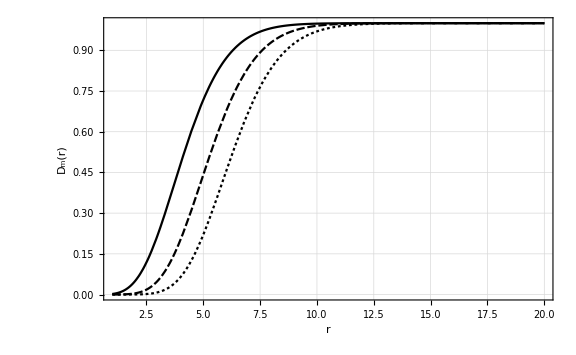

```mathematica
Plot[{DDSTriplet[6,r],DDSTriplet[8,r],DDSTriplet[10,r]},{r,1.0,20},Frame->True,GridLines->Automatic,ImageSize->Large,FrameLabel->{"r","D_m(r)"},LabelStyle->Medium]
```

Singlet and triplet potentials from Le Roy code:

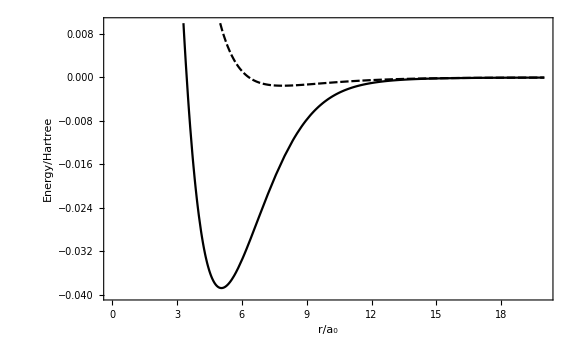

```mathematica
Singlet = Interpolation[Import["/Users/alysonlaskowski/LiScattering/fort.10"]];
Triplet = Interpolation[Import["/Users/alysonlaskowski/LiScattering/fort.30"]];
Plot[{Singlet[r],Triplet[r]},{r,1.0,20},Frame->True,PlotRange->{-0.040,0.010},ImageSize->Large,FrameLabel->{"r/a_0","Energy/Hartree"},LabelStyle->Large]
```

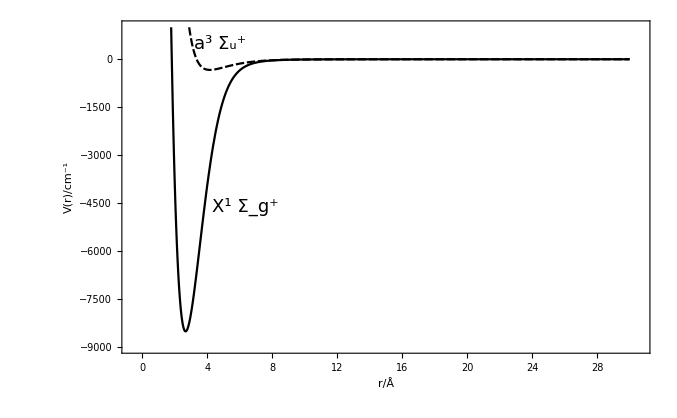

MLR Singlet and Triplet Potentials

i. Define well depths D_e, equilibrium internuclear distances r_e, reference distance r_ref, and coefficients in long-range interaction (energy in cm^-1 and length in Å)

```mathematica
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
t10 = 2.78683*10^9;
```

i.a Conversions between cm^-1and Hartree and Å and a_0

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
```

ii. Define parameters p and q used in radial variable y(r), ρ used in damping functions, and β coefficients

```mathematica
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
```

iii. Setup functions for β(r), y(r), and u_LR(r)

```mathematica
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
Clear[βinf]
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
β[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

iii.a Find β_∞for a^3 Σ_u^+and compare to value of Le Roy code

```mathematica
βinfT=βinf[tde,tre,DDSTriplet[6,tre],DDSTriplet[8,tre],DDSTriplet[10,tre],tc6,tc8,t10]
```

-0.509836

This matches Le Roy’s value. Now construct β(r) and u_LR(r) for the triplet potential, the latter of which includes Douketis type damping functions. Then set-up the triplet MLR potential

```mathematica
βTriplet[r_]:= βinfT*y[tref,r,5]+(1-y[tref,r,5])*Sum[tβcf[[j+1]]*y[tref,r,3]^j,{j,0,Length[tβcf]-1}];
ulrTriplet[r_]:= DDSTriplet[6,r] tc6/r^6+DDSTriplet[8,r] tc8/r^8+DDSTriplet[10,r] t10/r^10;
```

```mathematica
TripletMLR[r_]:= tde(1-ulrTriplet[r]/ulrTriplet[tre]*Exp[-βTriplet[r]*y[tre,r,p]])^2-tde;
```

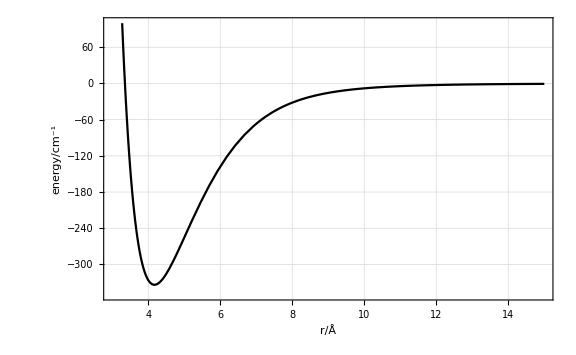

```mathematica
Plot[TripletMLR[r],{r,3.0,15},PlotRange->{-350,100},GridLines->Automatic,Frame->True,FrameLabel->{"r/Å","energy/cm^-1"},LabelStyle->Medium,ImageSize->Large]
```

iii.b MLR potential function for the X^1 Σ_g^+state

```mathematica
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
```

```mathematica
SingletMLR[r_]:= VMLR[r,sre,sde,β[r,sβcf1,βinf[sde,sre,1,1,1,C6,C8,C10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,C6,C8,C10]
```

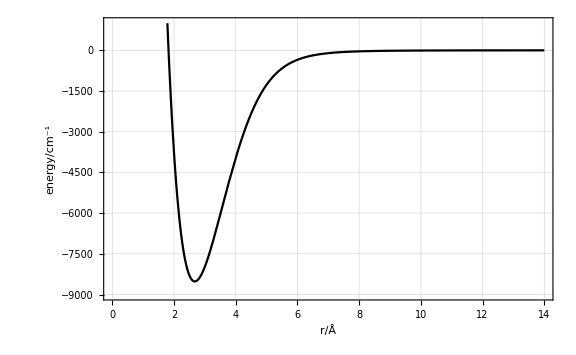

```mathematica
Plot[{SingletMLR[r]},{r,1.5,14},Frame->True,FrameLabel->{"r/Å","energy/cm^-1"},PlotStyle->{Red,Black},PlotRange->{-9000,1000},LabelStyle->Medium,ImageSize->Large,GridLines->Automatic,ImageSize->Large]
```

iii.c Check that our MLR functions match the potentials from the Le Roy code

```mathematica
Rmax=150;
Rmin=0.05;
NR =100000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
```

```mathematica
TripletMLRdat = Table[{RGrid[[i]],TripletMLR[RGrid[[i]]]},{i,1,NR}];
```

```mathematica
TripletMLRHBdat =Table[{RGrid[[i]]*AngstrominBohr,TripletMLRdat[[i,2]]*invcminHartree},{i,1,NR}];
```

```mathematica
TripletHBMLR=Interpolation[TripletMLRHBdat]
```

InterpolatingFunction[{{0.09732, 283.459}}, <>]

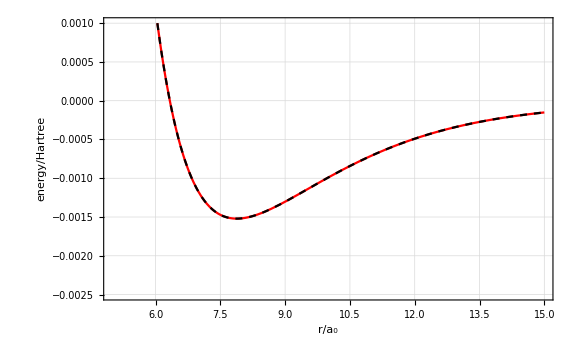

```mathematica
Plot[{TripletHBMLR[r],Triplet[r]},{r,5.0,15},PlotRange->{-0.0025,0.001},ImageSize->Large,PlotStyle->{Red,Dashed},GridLines->Automatic,Frame->True,FrameLabel->{"r/a_0","energy/Hartree"},LabelStyle->Medium]
```

The triplet MLR function matches Le Roy’s curve for the a^3 Σ_u^+state! Now for the singlet,

```mathematica
SingletMLRdat = Table[{RGrid[[i]],SingletMLR[RGrid[[i]]]},{i,1,NR}];
SingletMLRHBdat =Table[{RGrid[[i]]*AngstrominBohr,SingletMLRdat[[i,2]]*invcminHartree},{i,1,NR}];
SingletHBMLR=Interpolation[SingletMLRHBdat]
```

InterpolatingFunction[{{0.09732, 283.459}}, <>]

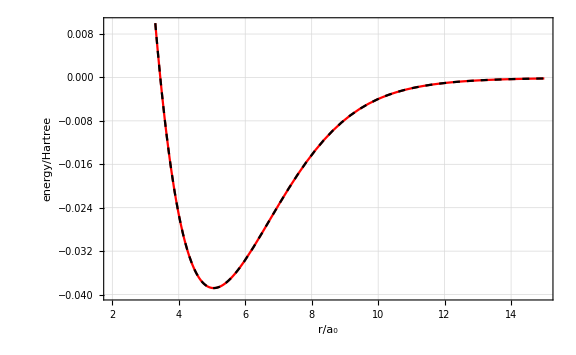

```mathematica
Plot[{SingletHBMLR[r],Singlet[r]},{r,2.0,15},PlotRange->{-0.040,0.010},ImageSize->Large,PlotStyle->{Red,Dashed},GridLines->Automatic,Frame->True,FrameLabel->{"r/a_0","energy/Hartree"},LabelStyle->Medium]
```

The singlet MLR function and Le Roy’s X^1 Σ_g^+ curve also match!

### Li + Li Collisions

Sources:

McAlexander Thesis

Julienne and Hutson, Phys. Rev. A 89, 052715 (2014)

The full Hamiltonian for a Li_2collision is

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

here P_0 and P_1 are the singlet and triplet projection operators, V_0(r) is the potential for the X^1(Σ^+)_g state, V_1(r) is the potential for the a^3(Σ^+)_u state, μ_B is the Bohr magneton, μ_N is the nuclear magneton, B is the magnitude of an external magnetic field, applied along the z-axis, g_s is the electronic gyromagnetic ratio, g_i is the nuclear gyromagnetic ratio, A is the hyperfine constant, s is the electronic spin, i is the nuclear spin, s_z is the component of electronic spin along the z-axis, i_z is the component of the nuclear spin along the z-axis, and the sum is over the two atoms.

Define electronic spin, nuclear spin, hyperfine constant, gyromagnetic ratios for electron and nucleus, nuclear and Bohr magnetons for 7-Li and 6-Li:

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;
```

Hyperfine constants in THz:

```mathematica
Li7A = 401.75204335 * 10^-6;
Li6A = 152.0*10^-6;
```

Hyperfine constants in cm^-1:

```mathematica
Li7Acm = (Li7A *6.626*10^-34*10^12)/(1.986*10^-23);
Li6Acm = (Li6A *6.626*10^-34*10^12)/(1.986*10^-23);
```

Hyperfine constants in Hartree:

```mathematica
Li7AH = Li7A*invcminHartree;
Li6AH = Li6A*invcminHartree;
```

Nuclear and Bohr Magnetons in units THz/G:

```mathematica
μb = (9.27*10^-24)/(6.626*10^-34)*10^-12*(1/10^4)
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4)
```

1.39903×10^-6

7.62267×10^-10

Nuclear and Bohr Magnetons in cm^-1/G:

```mathematica
μbcm = (μb *6.626*10^-34*10^12)/(1.986*10^-23)
μncm = (μn *6.626*10^-34*10^12)/(1.986*10^-23)
```

0.0000466767

2.54319×10^-8

Nuclear and Bohr Magnetons in Hartree/G:

```mathematica
μbH=μbcm*invcminHartree
μnH=μncm*invcminHartree
```

2.12675×10^-10

1.15876×10^-13

Hyperfine basis for ^7 Li_2

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

For M_T=2

```mathematica
mF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
```

Unsymmetrized Basis

```mathematica
mF2unsym =Select[f1m1f2m2basis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

```mathematica
mF2sym = Table[MatrixForm[mF2unsym[[i]]]+MatrixForm[Flatten[{mF2unsym[[i,3;;4]],mF2unsym[[i,1;;2]]}]],{i,1,Length[mF2unsym]}]
```

{(1
0
2
2)+(2
2
1
0),2 (1
1
1
1),(1
1
2
1)+(2
1
1
1),(2
0
2
2)+(2
2
2
0),(1
1
2
1)+(2
1
1
1),2 (2
1
2
1),(1
0
2
2)+(2
2
1
0),(2
0
2
2)+(2
2
2
0)}

Symmetrized Basis

```mathematica
DeleteDuplicates[mF2sym]
```

{(1
0
2
2)+(2
2
1
0),2 (1
1
1
1),(1
1
2
1)+(2
1
1
1),(2
0
2
2)+(2
2
2
0),2 (2
1
2
1)}

##### Singlet and triplet projection operators in hyperfine basis (given in Appendix B of McAlexander Thesis):

1. First expand the hyperfine basis into a linear combination of the molecular basis (i.e. the basis with S = s_1+s_2, I = i_1+i_2, m_S, and m_I as “good” quantum numbers) which are eigenstates of the triplet and singlet operators:

|f_1 m_f_1 f_2 m_f_2⟩ = ∑⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ |S m_s I m_I⟩

where ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ is the Clebsch-Gordan coefficient and is found by the following procedure:

1.a) De-couple |f_1 m_f_1 f_2 m_f_2⟩ basis into the atomic basis (i.e. the basis with m_s_1, m_s_2, m_i_1, and m_i_2 as “good” quantum numbers) through the expression:

|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2)|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩

1.b) Re-couple the atomic basis |s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩ to the molecular basis |S m_s I m_I⟩:

|s_1 m_s_1 i_1 m_i_1 s_2 m_s_2 i_2 m_i_2⟩=∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.c) Use the expressions of (1.a) and (1.b) to express the hyperfine basis  |f_1 m_f_1 f_2 m_f_2⟩ in terms of the molecular basis |S m_s I m_I⟩ :

|f_1 m_f_1 f_2 m_f_2⟩ =(-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I)|S m_s I m_I⟩

1.d) Take the inner product with |S' m_s'I 'm_I'⟩ to find an expression for ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩ = (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) ∑_(S,m_S,I,m_I) (-1)^(-m_S-m_I)√((2S+1)(2I+1))(s_1 | s_2
m_s_1 | m_s_2 S
-m_S)(i_1 | i_2
m_i_1 | m_i_2 I
-m_I) ⟨S' m_s'I 'm_I'|S m_s I m_I⟩

= (-1)^(2 i_2-2 s_1-m_1-m_2)√((2 f_1+1)(2 f_2+1)) ∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (-1)^(-m_S'-m_I')√((2S'+1)(2I'+1))(s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

⟨S' m_s'I 'm_I'|f_1 m_f_1 f_2 m_f_2⟩= ((-1)^(2 i_2-2 s_1-m_1-m_2))^(-m_S'-m_I')√((2 f_1+1)(2 f_2+1)(2S'+1)(2I'+1))∑_(m_(s_1,)m_s_2, m_i_1, m_i_2) (s_1 | i_1
m_s_1 | m_i_1 f_1
-m_1)(s_2 | i_2
m_s_2 | m_i_2 f_2
-m_2) (s_1 | s_2
m_s_1 | m_s_2 S'
-m_S')(i_1 | i_2
m_i_1 | m_i_2 I'
-m_I')

2. Using Eq. 23 with the Clebsch-Gordan coefficients given by Eq. 29, determine the matrix elements ⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ for the projection operators in the hyperfine basis:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| P_(0 or 1)|S m_s I m_I⟩

The projection operator P_(0 or 1) acts on the state |S m_s I m_I⟩ like a delta function where P_0=δ_(S,0) and P_1=δ_(S,1), and thus the matrix elements are:

⟨f_1'm_f_1'f_2'm_f_2'|P_(0 or 1)|f_1 m_f_1 f_2 m_f_2⟩ = ∑_(S,m_S,I,m_I) ∑_(S',m_S',I,'m_I') ⟨S' m_s'I 'm_I'|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ ⟨S' m_s'I 'm_I'| δ_(S, 0 or 1)|S m_s I m_I⟩

= ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0 or 1)

Note that the above expression only holds for an unsymmetrized basis set. For a symmetrized basis set with states {αβ=(αβ±(-1)^l βα)/(√(2(1+δ_αβ))) the elements of the projection operator P_(0 or 1) are:

{α'β'}P_(0 or 1){αβ}={α'β'}P_(0 or 1)(αβ±(-1)^l βα)/(√(2(1+δ_αβ)))

=1/(√(2(1+δ_αβ)))({α'β'}P_(0 or 1)αβ±(-1)^l{α'β'}P_(0 or 1)βα)

=1/(√(2(1+δ_αβ)))1/(√(2(1+δ_α'β')))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα).

Can this expression be simplified further? What are the relationships between α'β' P_(0 or 1)αβ, β'α' P_(0 or 1)βα, β'α' P_(0 or 1)αβ and α'β' P_(0 or 1)βα?

Define the exchange operator, 𝒫, which interchanges two particles:

𝒫αβ=βα

where α corresponds to particle 1 and β to particle 2 in αβ and vice versa in βα. Moreover, if we apply 𝒫 twice to αβ, we should find that the system returns to its original state:

𝒫^2 αβ=αβ.

Therefore, 𝒫^2=1 and it follows that the eigenvalues of 𝒫 are ±1. If the particles are identical, the Hamiltonian must treat them the same, and thus, 𝒫 and H are compatible observables: [𝒫,H]=0 and we can find a complete set of functions that are simultaneous eigenstates of both. These solutions can be either symmetric (eigenvalue +1; for bosons) or antisymmetric (eigenvalue -1; for fermions) under exchange:

𝒫{αβ}=±αβ=βα→ αβ=±βα.

Using the above relationship, we can rewrite the matrix element β'α' P_(0 or 1)βα as

α'β' P_(0 or 1)αβ=±β'α' P_(0 or 1)±βα=β'α' P_(0 or 1)βα

and simplify our expression for {α'β'}P_(0 or 1){αβ} to

{α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(2α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα).

Similarly, the matrix element β'α' P_(0 or 1)αβ can be rewritten as

β'α' P_(0 or 1)αβ=±α'β' P_(0 or 1)±βα=α'β' P_(0 or 1)βα.

This simplifies {α'β'}P_(0 or 1){αβ} further to

{α'β'}P_(0 or 1){αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ).

Function to calculate coefficients ⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩ :

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];

ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];
```

Singlet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 0) (for unsymmetrized basis, i.e., used for distinguishable particles):

```mathematica
SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];
```

For symmetrized basis; p=0 corresponds to bosons, p=1 to fermions

I. Using  {α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ+β'α' P_(0 or 1)βα±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

```mathematica
SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi7=FullSimplify[SingletProjectionSym[0,0]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1/2,-1/2},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
N[MatrixForm[SProjSymLi7]]
```

(0.1875 | 0.153093 | -0.216506 | 0.216506 | -0.1875
0.153093 | 0.125 | -0.176777 | 0.176777 | -0.153093
-0.216506 | -0.176777 | 0.25 | -0.25 | 0.216506
0.216506 | 0.176777 | -0.25 | 0.25 | -0.216506
-0.1875 | -0.153093 | 0.216506 | -0.216506 | 0.1875)

```mathematica
MatrixForm[SProjSymLi7.SProjSymLi7]
```

(3/16 | (√(3/2))/8 | -(√3)/8 | (√3)/8 | -3/16
(√(3/2))/8 | 1/8 | -1/(4 √2) | 1/(4 √2) | -(√(3/2))/8
-(√3)/8 | -1/(4 √2) | 1/4 | -1/4 | (√3)/8
(√3)/8 | 1/(4 √2) | -1/4 | 1/4 | -(√3)/8
-3/16 | -(√(3/2))/8 | (√3)/8 | -(√3)/8 | 3/16)

II. Using {α'β'}P_(0 or 1){αβ}=1/2 1/(√(1+δ_αβ)(1+δ_α'β'))(2α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ±(-1)^l α'β' P_(0 or 1)βα)

```mathematica
SingletProjectionSym2[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(2 ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi72=FullSimplify[SingletProjectionSym2[0,0]];
```

```mathematica
MatrixForm[SProjSymLi7-SProjSymLi72]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

Expression (I) and (II) for the singlet projection operator are equivalent.

III. Using {α'β'}P_(0 or 1){αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))(α'β' P_(0 or 1)αβ±(-1)^l β'α' P_(0 or 1)αβ)

```mathematica
SingletProjectionSym3[p_,l_]:= Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
SProjSymLi73=FullSimplify[SingletProjectionSym3[0,0]];
```

```mathematica
MatrixForm[SProjSymLi73-SProjSymLi7]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

Expression (III) for the singlet projection operator is equivalent to (I) and (II)

Triplet Projection Matrix with elements  ∑_(S,m_S,I,m_I) ⟨S m_s I m_I|f_1'm_f_1'f_2'm_f_2'⟩⟨S m_s I m_I|f_1 m_f_1 f_2 m_f_2⟩δ_(S, 1) (for unsymmetrized basis):

```mathematica
TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];
```

For symmetrized basis:

```mathematica
TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]),{j,1,5},{jp,1,5}]
```

```mathematica
TProjSymLi7=FullSimplify[TripletProjectSym[0,0]];
```

$Aborted

```mathematica
N[MatrixForm[TProjSymLi7]]
```

(0.8125 | -0.153093 | 0.216506 | -0.216506 | 0.1875
-0.153093 | 0.875 | 0.176777 | -0.176777 | 0.153093
0.216506 | 0.176777 | 0.75 | 0.25 | -0.216506
-0.216506 | -0.176777 | 0.25 | 0.75 | 0.216506
0.1875 | 0.153093 | -0.216506 | 0.216506 | 0.8125)

```mathematica
MatrixForm[TProjSymLi7.TProjSymLi7]
```

(13/16 | -(√(3/2))/8 | (√3)/8 | -(√3)/8 | 3/16
-(√(3/2))/8 | 7/8 | 1/(4 √2) | -1/(4 √2) | (√(3/2))/8
(√3)/8 | 1/(4 √2) | 3/4 | 1/4 | -(√3)/8
-(√3)/8 | -1/(4 √2) | 1/4 | 3/4 | (√3)/8
3/16 | (√(3/2))/8 | -(√3)/8 | (√3)/8 | 13/16)

Combined Zeeman and Hyperfine Interactions (From McAlexander Appendix E)

McAlexander Eq. E.2

(s i)f'm' H^HZ(s i)f m=A^HF/2[f(f+1)-s(s+1)-i(i+1)]δ_ff' δ_mm'+g_s μ_B B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_s(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'+g_i μ_N B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_i(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√(1+δ_αβ)(1+δ_α'β'))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7[B_]:=FullSimplify[HZsym[0,0,B]];
```

```mathematica
MatrixForm[HZsymLi7[B]]
```

(-4.57629×10^-9-2.12046×10^-10 B | 2.60318×10^-10 B | 0. | 0. | 0
2.60318×10^-10 B | -9.15259×10^-10+5.03113×10^-13 B | 0. | 0. | 2.60318×10^-10 B
0. | 0. | -9.15259×10^-10+2.13052×10^-10 B | 0.+2.12549×10^-10 B | 0.
0. | 0. | 0.+2.12549×10^-10 B | 2.74578×10^-9+2.13052×10^-10 B | 0.
0 | 2.60318×10^-10 B | 0. | 0. | 2.74578×10^-9+2.13052×10^-10 B)

```mathematica
Htest[r_,B_]:= HZsymLi7[B]+TProjSymLi7*Triplet[r]+SProjSymLi7*Singlet[r];
```

```mathematica
SingletMatrix2[r_]:= HZsymLi7[0]+SProjSymLi7 Singlet[r];
TripletMatrix2[r_]:= HZsymLi7[0]+TProjSymLi7 Triplet[r];
```

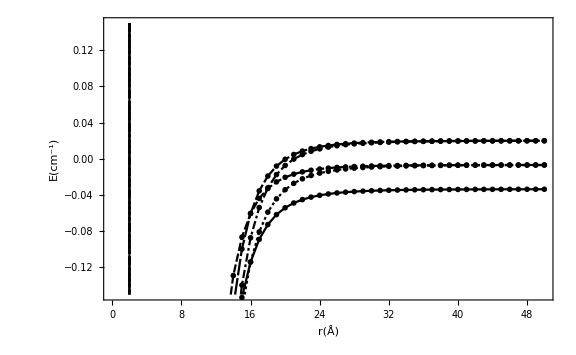

```mathematica
ListLinePlot[{Table[{j, SingletMatrix2[j][[1, 1]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[2, 2]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[3, 3]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[4, 4]]}, {j, 1, 50}], Table[{j, SingletMatrix2[j][[5, 5]]}, {j, 1, 50}]},ImageSize->Large,Frame->True,FrameLabel->{"r(Å)","E(cm^-1)"},LabelStyle->Medium,PlotRange->{-0.15,0.15}]
```

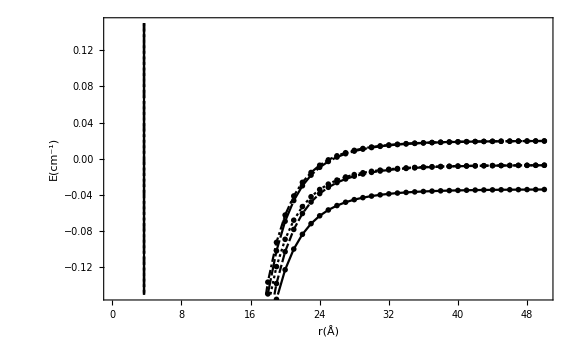

```mathematica
ListLinePlot[{Table[{j, TripletMatrix2[j][[1, 1]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[2, 2]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[3, 3]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[4, 4]]}, {j, 1, 50}], Table[{j, TripletMatrix2[j][[5, 5]]}, {j, 1, 50}]},ImageSize->Large,Frame->True,FrameLabel->{"r(Å)","E(cm^-1)"},LabelStyle->Medium,PlotRange->{-0.15,0.15}]
```

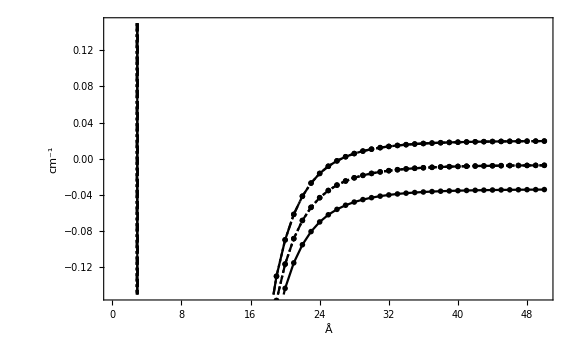

```mathematica
ListLinePlot[{Table[{j, Htest[j, 0][[1, 1]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[2, 2]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[3, 3]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[4, 4]]}, {j, 1, 50}], Table[{j, Htest[j, 0][[5, 5]]}, {j, 1, 50}]},Frame->True,ImageSize->Large,FrameLabel->{"Å","cm^-1"},PlotRange->{-0.15,0.15},LabelStyle->Large]
```

```mathematica
ListLinePlot[{Table[{j, Htest[50, j][[1, 1]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[2, 2]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[3, 3]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[4, 4]]}, {j, 1, 1000}], Table[{j, Htest[50, j][[5, 5]]}, {j, 1, 1000}]},  ImageSize-> Large, Frame ->True, FrameLabel ->{"B(G)", "E(cm^-1)" }, LabelStyle ->Medium]
```

Single Channel Calculation Using {2222} state of ^7 Li +^7 Li

{2222} is a pure triplet with m_F=m_1+m_2=m_S+m_I=4. Moreover, it is the only symmetrized state with m_F=4, and thus, it is not coupled to any other {f_1 m_1 f_2 m_2}. (From McAlexander thesis, “the coupled-channel Hamiltonian will only couple a channel to those channels with the same total spin projection”(pp. 50).) The Hamiltonian for this state is given by

H = -ℏ^2/(2μ) d^2/(d r^2)+ H_1^HZ+H_2^HZ+V_1(r)+(l(l+1)ℏ^2)/(2 μr^2)

=-ℏ^2/(2μ) d^2/(d r^2)+ 2 H_1^HZ+V_1(r)+(l(l+1)ℏ^2)/(2 μr^2)

where H_1^HZ=H_2^HZ because f_1=f_2 and m_1=m_2.

```mathematica
2*HZ[2,2,2,2,Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]
```

2 (1.37289×10^-9+2.13052×10^-10 B)

```mathematica
ProjectionMatrixElement[2,2,2,2,2,2,2,2,Li7s,Li7i,Li7s,Li7i,0]
```

0

```mathematica
ProjectionMatrixElement[2,2,2,2,2,2,2,2,Li7s,Li7i,Li7s,Li7i,1]
```

1

The singlet projection operator should be zero and the triplet projection operator should be one if {2222} is a pure triplet.

```mathematica
HLi7mF4[r_,l_,B_]:= 2*HZ[2,2,2,2,Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]+Triplet[r]+(l(l+1))/r^2;
```

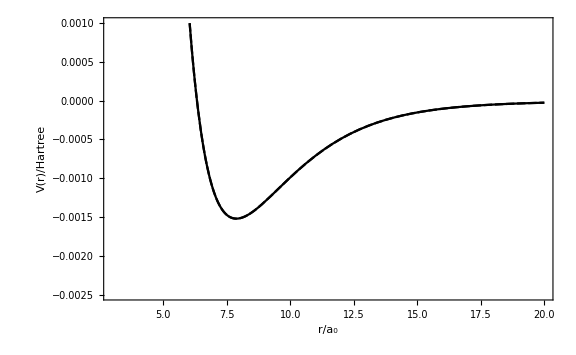

```mathematica
Plot[{HLi7mF4[r,0,0],Triplet[r]},{r,3.0,20},Frame->True,FrameLabel->{"r/a_0","V(r)/Hartree"},ImageSize->Large,LabelStyle->Medium,PlotRange->{-0.0025,0.001}]
```

Modules to calculate cotδ_0, the scattering length, and effective range

```mathematica
CalcCotanDelta[Εtest_,rmax_,rmin_,μ_,ℏ_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-ℏ^2/(2 μ)u''[r]+TripletHBMLR[r] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERE[rmax_,rmin_,ΕMin_,ΕMax_,μ_,ℏ_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDelta[Εtest,rmax,rmin,μ,ℏ]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
Clear[ksqr,rmin,rmax]
```

```mathematica
rmin =2.0;
rmax = 250;
EMin = 0.000000001;
EMax =0.0000001 ;
amu = (1.66053906660 10^-27)/(9.1093837015 10^-31);
massLi7=7.016004amu;
μ=massLi7/2;
ℏ =1;
Εtest = 10^-16;
```

```mathematica
soltp = NDSolveValue[{-ℏ^2/(2 μ)u''[r]+ TripletHBMLR[r]*u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
```

```mathematica
soltpdr[r_]:=D[soltp[rp],rp]/.rp->r;
```

```mathematica
solsg = NDSolveValue[{-ℏ^2/(2 μ)u''[r]+ Singlet[r]*u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
Plot[{soltp[r],soltpdr[r]},{r,rmin,250},Frame->True,ImageSize->Large,GridLines->Automatic]
```

-Graphics-

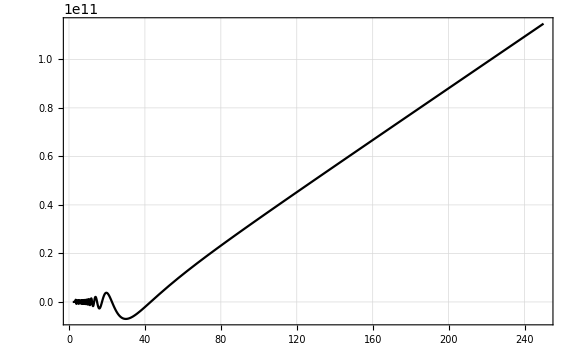

```mathematica
Plot[{solsg[r]},{r,rmin,250},Frame->True,ImageSize->Large,GridLines->Automatic]
```

```mathematica
CalcCotanDelta[Εtest,rmax,rmin,μ,ℏ]
```

32273.9

```mathematica
1/32273.9
```

0.0000309848

```mathematica
{ascat,reff,EREData}=CalcERE[500,rmin,10^-12,10^-11,μ,ℏ]
```

{-27.8339,486.061,{{1.27894×10^-8,0.0359306},{2.42998×10^-8,0.0359334},{3.58103×10^-8,0.0359362},{4.73208×10^-8,0.035939},{5.88312×10^-8,0.0359417},{7.03417×10^-8,0.0359445},{8.18521×10^-8,0.0359474},{9.33626×10^-8,0.0359502},{1.04873×10^-7,0.035953},{1.16383×10^-7,0.0359558},{1.27894×10^-7,0.0359585}}}

Triplet scattering length is in agreement with the value quoted in McAlexander thesis, a_T=-27 a_0, and Julienne and Hutson Phys. Rev. A 89, 052715 (2014), a_T=-26.92 a_0.

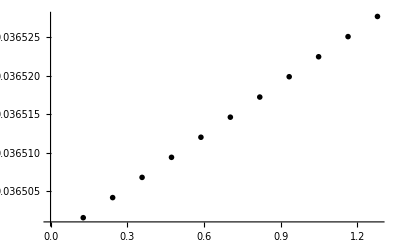

```mathematica
ListPlot[EREData]
```

#### Single Channel Scattering Calculation Using QDT

I. Define zero-energy solution and Riccati functions

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2)];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=(*√(k/π)*)r SphericalBesselJ[l,k r];
g[l_,k_,r_]:=(*√(k/π)*)r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=Simplify[D[f[l,k,rp],rp]]/.rp->r; 
dgdr[l_,k_,r_]:=Simplify[D[g[l,k,rp],rp]]/. rp->r;
```

II. Define reference wave-function base pairs

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=-α[r]Cos[ϕ+phaseint[r]];
f0=α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

III. Calculate alpha and phase integral functions using the Milne method. These will then be used for constructing the reference wave functions f^o and g^o in the long range-region.

```mathematica
CalcAlphaPhaseIntFun[Ε_,l_,rx_,rf_,r_,nr_]:= Module[{k,BC1,BC2,asol,rGrid,PhaseIntTable,rp,PhaseIntFun,αfun,α},
k=Sqrt[2 μ (Ε-TripletHBMLR[r])];
BC1 = 1/Sqrt[k^(1/2)]/.r->rx;
BC2 = D[1/Sqrt[k^(1/2)],r]/.r->rx;
asol = NDSolve[{α''[r] + k^2 α[r] -1/α[r]^3== 0, α[rx] == BC1, α'[rx] == BC2},α,{r,rx,rf}];
rGrid = Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable = Flatten[{0,Table[NIntegrate[1/α[rp]^2/.asol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
PhaseIntFun = Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[1;;i]]]},{i,1,nr}]];
αfun = α/.asol;
Flatten[{αfun,PhaseIntFun}]
];
```

IV. Calculation of log-derivative of the interior solution at the matching radius.

```mathematica
CalcY[Ε_,l_,rmin_,rmax_,μ_,r0_]:=Module[{Y,u,up,rp,r},
u=NDSolveValue[{-1/(2 μ)u''[r]+ TripletHBMLR[r]*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up[r_] = D[u[rp],rp]/.rp->r;
Y = up[r]/u[r]/.r->r0;
Return[Y]
]
```

V. Calculation of ϕ which ensures maximum linear independence of reference wave functions.

```mathematica
ksqr[Ε_,l_,r_] := (Ε - TripletHBMLR[r]);
BC1[Ε_,l_,r_,rx_] := 1/Sqrt[(Ε - TripletHBMLR[r])^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_] := D[1/Sqrt[(Ε - TripletHBMLR[r])^(1/2)],r]/.r->rx;
Εtest=10^-16;
rx=8.0;
rf=250;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Εtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Εtest,ltest,r,rx],α'[rx]==BC2[Εtest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,20}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,20}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,20}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,20}],{rf,rGrid}]];
ϕfinal=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
ϕfinal[[1]]
```

0.126247

VI. Short-range K-matrix module

```mathematica
CalCKsr[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rmin_,rmax_,μ_]:= Module[{Y,kin,f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun},
Y=CalcY[Ε,l,rmin,rmax,μ,r0];
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFun[Ε,l,rx,rf,r,nr];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = (Y f0 -f0p)/(Y g0 -g0p)/. r->r0;
Return[Ksr]
]
```

VII. Physical K-matrix module

```mathematica
CalcK[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rfinal_,rmin_,rmax_,μ_]:= Module[{f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun,K,k,F,dF,G,dG},
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFun[Ε,l,rx,rf,r,nr];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = CalCKsr[Ε,r0,l,rx,rf,nr,r,ϕ,rmin,rmax,μ];
k = Sqrt[2 μ Ε];
F = f[l,k,r];
dF = dfdr[l,k,r];
G = g[l,k,r];
dG = dgdr[l,k,r];
K = ((f0 dF - f0p F) - Ksr (g0 dF - g0p F))/((f0 dG - f0p G) - Ksr (g0 dG - g0p G))/.r->rfinal;
K
]
```

```mathematica
ltest = 0;
r0 = 30.0;
rfinal = 250;
```

```mathematica
-CalcK[Εtest,r0,ltest,rx,rf,nr,r,ϕfinal[[1]],rfinal,rmin,rfinal,μ]/Sqrt[2 μ Εtest]
```

-27.4408

This value for a_T is in agreement with our previous result! Now for the singlet...

Calculate alpha and phase integral functions using the Milne method. These will then be used for constructing the reference wave functions f^o and g^o in the long range-region.

```mathematica
CalcAlphaPhaseIntFunSinglet[Ε_,l_,rx_,rf_,r_,nr_]:= Module[{k,BC1,BC2,asol,rGrid,PhaseIntTable,rp,PhaseIntFun,αfun,α},
k=Sqrt[2 μ (Ε-SingletHBMLR[r])];
BC1 = 1/Sqrt[k^(1/2)]/.r->rx;
BC2 = D[1/Sqrt[k^(1/2)],r]/.r->rx;
asol = NDSolve[{α''[r] + k^2 α[r] -1/α[r]^3== 0, α[rx] == BC1, α'[rx] == BC2},α,{r,rx,rf}];
rGrid = Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable = Flatten[{0,Table[NIntegrate[1/α[rp]^2/.asol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
PhaseIntFun = Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[1;;i]]]},{i,1,nr}]];
αfun = α/.asol;
Flatten[{αfun,PhaseIntFun}]
];
```

Calculation of log-derivative of the interior solution at the matching radius.

```mathematica
CalcYSinglet[Ε_,l_,rmin_,rmax_,μ_,r0_]:=Module[{Y,u,up,rp,r},
u=NDSolveValue[{-1/(2 μ)u''[r]+ SingletHBMLR[r]*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up[r_] = D[u[rp],rp]/.rp->r;
Y = up[r]/u[r]/.r->r0;
Return[Y]
]
```

V. Calculation of ϕ which ensures maximum linear independence of reference wave functions.

```mathematica
ksqrSinglet[Ε_,l_,r_] := (Ε - SingletHBMLR[r]);
BC1Singlet[Ε_,l_,r_,rx_] := 1/Sqrt[(Ε - SingletHBMLR[r])^(1/2)]/.r->rx;
BC2Singlet[Ε_,l_,r_,rx_] := D[1/Sqrt[(Ε - SingletHBMLR[r])^(1/2)],r]/.r->rx;
Εtest=10^-16;
rxSinglet=5.0;
rf=250;
α0solSinglet=Flatten[Table[NDSolve[{α''[r]+ksqrSinglet[Εtest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1Singlet[Εtest,ltest,r,rx],α'[rx]==BC2Singlet[Εtest,ltest,r,rx]},α,{r,rxSinglet,rf}],{ltest,0,20}]];
α0funSinglet=Table[α/.α0solSinglet[[i]],{i,1,Length[α0solSinglet]}];
nr=300;rGrid=Table[rxSinglet+((i-1)/(nr-1))^3(rf-rxSinglet),{i,1,nr}];
PhaseIntTableSinglet=Table[Flatten[{0,Table[NIntegrate[(α0funSinglet[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,20}];
phaseintfunSinglet=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTableSinglet[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,20}];
phivalsSinglet=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0funSinglet[[ltest+1]],phaseintfunSinglet[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,20}],{rf,rGrid}]];
ϕfinalSinglet=Table[phivalsSinglet[[i,nr,2]],{i,1,Length[phivalsSinglet]}];
```

```mathematica
ϕfinalSinglet[[1]]
```

0.16746

Short-range K-matrix module

```mathematica
CalCKsrSinglet[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rmin_,rmax_,μ_]:= Module[{Y,kin,f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun},
Y=CalcYSinglet[Ε,l,rmin,rmax,μ,r0];
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFunSinglet[Ε,l,rx,rf,r,nr];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = (Y f0 -f0p)/(Y g0 -g0p)/. r->r0;
Return[Ksr]
]
```

Physical K-matrix module

```mathematica
CalcKSinglet[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rfinal_,rmin_,rmax_,μ_]:= Module[{f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun,K,k,F,dF,G,dG},
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFunSinglet[Ε,l,rx,rf,r,nr];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = CalCKsrSinglet[Ε,r0,l,rx,rf,nr,r,ϕ,rmin,rmax,μ];
k = Sqrt[2 μ Ε];
F = f[l,k,r];
dF = dfdr[l,k,r];
G = g[l,k,r];
dG = dgdr[l,k,r];
K = ((f0 dF - f0p F) - Ksr (g0 dF - g0p F))/((f0 dG - f0p G) - Ksr (g0 dG - g0p G))/.r->rfinal;
K
]
```

```mathematica
-CalcKSinglet[Εtest,r0,ltest,rxSinglet,rf,nr,r,ϕfinalSinglet[[1]],rfinal,rmin,rfinal,μ]/Sqrt[2 μ Εtest]
```

34.5206

Singlet scattering length agrees with Julienne and Hutson Phys. Rev. A 89, 052715 (2014), a_s=34.331 a_0!